# 1. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime: Tatjana

Priimek:

Vpisna številka:

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [5 točk]

Izračunajte limito .

```mathematica
Limit[(1000^n+1024^n).08^(1/n), n-> ∞]
```

∞

## 2. naloga [15 točk]

Na neki točki boste spoznali Taylorjev razvoj eksponentne funkcije. Eksponentno funkcijo lahko namreč zapišemo kot funkcijsko potenčno vrsto oblike . Ta zapis nam pove, da lahko z delnimi vsotami  poljubno dobro aproksimiramo eksponentno funkcijo.
1. (5 točk) Izračunajte numerično vrednost delne vsote . Uporabite lahko funkcijo Factorial. Če želite, lahko prej definirate funkcijo iz naslednje naloge in jo uporabite.
2. (5 točk) Definirajte funkcijo delne vsote fn, ki sprejme parametra x in n in ima zgornji predpis. Funkcija naj vrača točne vrednosti, ne numeričnih približkov.
3. (5 točk) Narišite grafa eksponentne funkcije in tretje delne vsote na intervalu [-3,3] . Pri tem nastavite razmerje koordinatnih osi na automatic in zalogo vrednosti na [0,7].

```mathematica
ClearAll[x,k,n,e]
```

```mathematica
NSum[17^(-k)/(k!), {k,0,17}]
```

1.06059

```mathematica
fn[x_,n_]:=∑_(k=0)^n x^k/(k!)
```

```mathematica
NSum[17^(-k)/(k!), {k,0,17}]
```

1.06059

```mathematica
fn[x,17]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600+x^13/6227020800+x^14/87178291200+x^15/1307674368000+x^16/20922789888000+x^17/355687428096000

```mathematica
NSum[fn[x,n], {x,0,17}]
```

NSum::nsnum: Summand (or its derivative) fn[x,n] is not numerical at point x = 0.

NSum[fn[x,n],{x,0,17}]

```mathematica
fn[x,17]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600+x^13/6227020800+x^14/87178291200+x^15/1307674368000+x^16/20922789888000+x^17/355687428096000

```mathematica
fn[x,3]
```

1+x+x^2/2+x^3/6

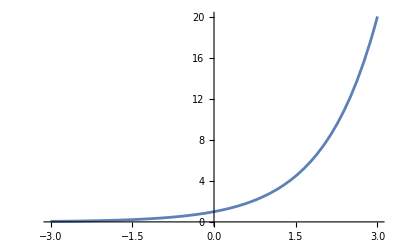

```mathematica
graf2=Plot[fn[x, Infinity],{x,-3,3}]
```

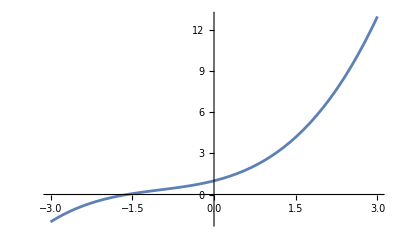

```mathematica
graf1=Plot[fn[x,3], {x,-3,3}]
```

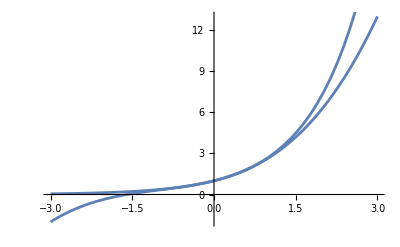

```mathematica
Show[graf1,graf2]
```

## 3. naloga [10 točk]

1. (5 točk) Definirajte funkcijo PetQ, ki sprejme parameter n in vrne True, če ima n natanko 5 deliteljev.
2. (5 točk) Izpišite vsa števila med 1 in 1000, ki imajo natanko 5 deliteljev.

```mathematica
ClearAll[n]
```

```mathematica
Petq1[n_]:=Length[Divisors[n]]
```

```mathematica
Petq1[16]
```

5

```mathematica
Petq[n_]:=TrueQ[Petq1[n]==5]
```

```mathematica
Petq[16]
```

True

```mathematica
Solve[ n,Petq1[n]==5]
```

Solve::naqs: n is not a quantified system of equations and inequalities.

Solve[n,True]

```mathematica
Select[Range[1,1000], Petq[n]]
```

{}